```mathematica
(*Parameters*)
δ=150; 
Dil=0.5; 
R0=1; 
ma=0.01; mb=0.1;mc=0.05; (*Example values for m parameters*)
TI=20;

(*Define Imax and m as before*)
Imax[T_]:=Exp[-((T-TI)^2)/δ];
m[T_]:=ma Exp[mb T]+mc;
Req:=m[T] R0/((1-δ) Imax[T]-m[T]);


(*Function for Ce*)
CeFunc[T_]:=Dil (S-Req)(Req + R0)/(Imax[T] Req);

(*Distributions for Req and T*)
sDist=NormalDistribution[1.5,0.2];  (*Example:Normal distribution for S*)
tDist=NormalDistribution[20,5]; (*Example:Uniform distribution for T*)

(*Perform a simulation with independent draws for Req and T*)
numSimulations=10000; (*Number of simulations*)

simulationResults=Table[Module[{S,T,Ce},(*Draw values for Req and T*)S=RandomVariate[sDist];
T=RandomVariate[tDist];
(*Calculate Ce based on S and T*)Ce=CeFunc[S,T];
{S,T,Ce}  (*Return the values*)],{numSimulations}];

(*Display the first few results*)
Take[simulationResults,10]
(*Calculate the 95th percentile*)
minValue=Min[simulationResults];
percentile95=Quantile[simulationResults[[All, 3]],0.95];
minValue
percentile95
```

{{1.45259,10.726,12.8027},{1.30089,23.6578,8.4108},{1.6615,16.5364,7.23464},{1.5466,13.7703,9.01466},{1.56104,24.0382,7.71745},{1.43909,24.8323,8.47694},{1.63072,18.6542,6.83277},{1.78023,14.3997,7.91115},{1.72411,22.2305,6.75848},{1.42925,16.2967,7.98103}}

-1.19068

13.6786

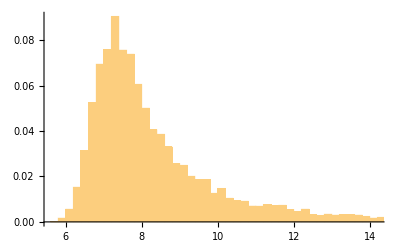

```mathematica
Histogram[simulationResults[[All,3]],500,"Probability"]
```

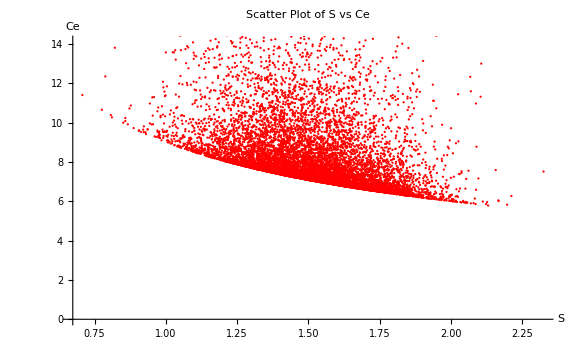

```mathematica
ListPlot[
simulationResults[[All,{1,3}]],
PlotStyle->Red,
AxesLabel->{"S","Ce"}, 
FrameLabel->{"S","Ce"},
LabelStyle->13,(*Increase the font size*)PlotLabel->Style["Scatter Plot of S vs Ce",20],(*Title of the plot*)TicksStyle->Directive[FontSize->15],(*Size of tick labels*)ImageSize->Large (*Makes the entire plot larger*)
]
```

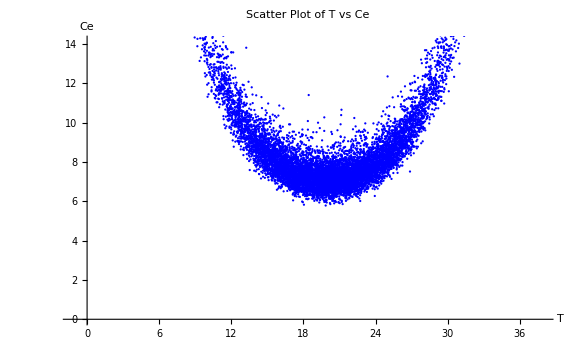

```mathematica
ListPlot[
simulationResults[[All,{2,3}]],
PlotStyle->Blue,
AxesLabel->{"T","Ce"}, 
FrameLabel->{"T","Ce"},
LabelStyle->13,(*Increase the font size*)PlotLabel->Style["Scatter Plot of T vs Ce",20],(*Title of the plot*)TicksStyle->Directive[FontSize->15],(*Size of tick labels*)ImageSize->Large (*Makes the entire plot larger*)
]
```

```mathematica
ListPlot3D[simulationResults,AxesLabel->{"S","T","Ce"},PlotStyle->Directive[PointSize[Medium],Blue],(*Customize point size and color*)LabelStyle->16,(*Make labels larger*)Boxed->True,ImageSize->Large,PlotRange->All
]
```

-Graphics3D-